```mathematica
Clear["Global`*"];
```

```mathematica
dx=2019;dy=1101;
```

```mathematica
(x+dx)(6a+b)−(y+dy)(11a+2b)==3a−183b//FullSimplify
```

(6 a+b) x==(11 a+2 b) y

```mathematica
d=Norm[{713,732}-{dx,dy}]
```

17 √6373

```mathematica
solxy=Solve[{x-d,y}.{1,k}==0&&y/2==k*(x+d)/2,{x,y}]//FullSimplify
```

{{x→-(17 √6373 (-1+k^2))/(1+k^2),y→(34 √6373 k)/(1+k^2)}}

```mathematica
xk=x/.solxy[[1]]
yk=y/.solxy[[1]]
```

-(17 √6373 (-1+k^2))/(1+k^2)

(34 √6373 k)/(1+k^2)

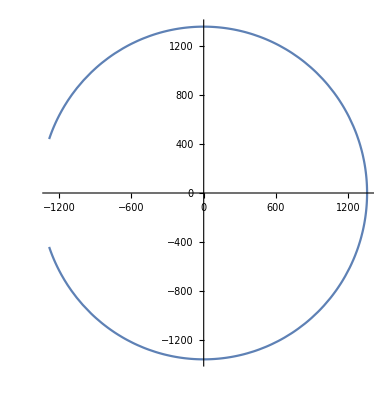

```mathematica
ParametricPlot[{xk,yk},{k,-6,6}]
```

```mathematica
r2=xk^2+yk^2//FullSimplify
```

1841797

```mathematica
A=Pi*r2
```

1841797 π